# Position projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,"TwoAhead"]:=ArrayPad[rho,{{0,4},{0,4}}]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]&[env["Unitary"][dim+1]]},
Inner[Chop[#1*ApplyOperator[#2[dim+1],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=ApplyOperator[#,DTQWSpacing[rho,env["Type"]]]&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*ApplyOperator[#2[Length[rho]/2+1],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,2*t],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,2*t],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
```

## DTQWQuanticity

```mathematica
DTQWQuanticity[coin_,range_]:=Module[{env,probs,sds,lm,nlm,p},
Table[
env=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1-p,p},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
probs=DTQWPosDistribution/@DTQWTrace[coin,100,env];
sds=DTQWPosStandardev/@probs;
lm=LinearModelFit[sds,x,x];
nlm=NonlinearModelFit[sds,A*Sqrt[x],{A},x];
{p,lm["AdjustedRSquared"],nlm["AdjustedRSquared"]},
{p,range}
]
]
(* Función incompleta, falta añadir funcionalidad usando la función para modificar envs *)
```

## DTQW Matrix Plot

```mathematica
DTQWMatrixPlot[c0_,n_,env_,h_]:=Module[{dmats},
dmats=MatrixPartialTrace[#,h,{Round[Length[#]/2],2}]&/@DTQWTrace[c0,n,env];
ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
PlotRange->{0,0.5},
Mesh->True,
MeshStyle->Black
]&/@Table[m,{m,Abs[dmats]}]
]
```

## Misc. functions

```mathematica
ApplyOperator[operator_?MatrixQ,rho_]:=operator.rho.ConjugateTranspose[operator]
ApplyOperator[operator_Function,rho_]:=operator[rho]
```

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=LinearModelFit[stdev,x,x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
DTQWSummary[coin_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,100,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
GraphicsRow[{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All
]
}]
]
```

## External stuff

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
DShiftOperator[n_]:=SparseArray[Join[Table[{i,i-2},{i,Range[4,#,2]}],Table[{i,i-4},{i,Range[5,#,2]}]]->1,{#,#}]&[2*n]
DUnitaryOperator[n_]:=DShiftOperator[n].CoinOperator[n]
PositionprojOperator[n_]:=Function[rho,DiagonalMatrix@Diagonal[rho]]
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
```

## Examples

```mathematica
coin={1,ⅈ}/Sqrt[2.];
```

```mathematica
envO0=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->(IdentityMatrix[2*#,SparseArray]&),
"Probabilities"->{0.5,0.5},
"Kraus"->{UnitaryOperator,DUnitaryOperator}
|>];
```

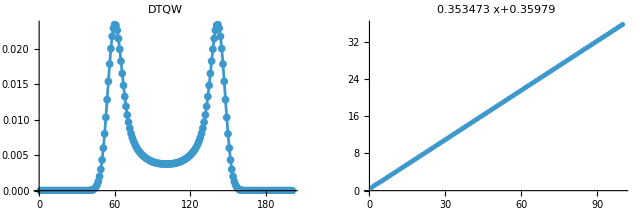

```mathematica
DTQWSummary[coinO0,envO0]
```

```mathematica
envO1=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
```

```mathematica
DTQWSummary[coinO1,envO1]
```

-Graphics-

```mathematica
DTQW[coin,100,envO0]==DTQW[coin,100,envO1]
```

True